We will do some basic math exercise here like plotting and all.

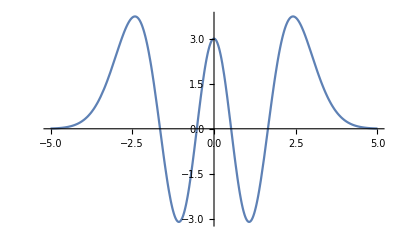

```mathematica
Plot[(4x^4-12x^2+3)Exp[-x^2/2],{x,-5,5}]
```

* All of Mathematica’s built-in function names begin with capital letters.
* Function arguments are closed in square brackets and separated by commas.
* “a*b” is same as “a b” but not “ab”. “ab” is just another variable.

Now we refactor the same code readability.

The semicolons serve as statement separators,and also suppress any displayed output of the
lines that precede them.

```mathematica
psi=(4x^4-12x^2+3)Exp[-x^2/2]; 
xmax = 5;
Plot[psi,{x,-xmax,xmax}]
```

-Graphics-

Because all of Mathematica’s built-in names (such as Plot and Exp) begin with
capital letters, it’s a good habit to begin all your own names (such as psi and
xMax) with lower-case letters. Then you can easily tell at a glance which names are
Mathematica’s and which are yours.

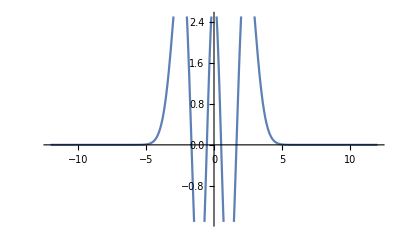

```mathematica
psi=(4x^4-12x^2+3)Exp[-x^2/2]; 
xmax = 12;
Plot[psi,{x,-xmax,xmax}]
(* See the peaks gets cut off. Use PlotRange to adjust that*)
```

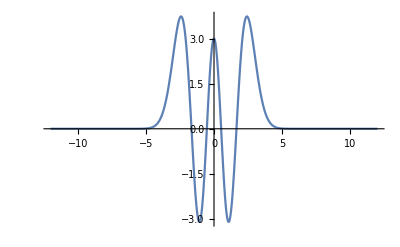

```mathematica
psi=(4x^4-12x^2+3)Exp[-x^2/2]; 
xmax = 12;
Plot[psi,{x,-xmax,xmax},PlotRange->All]
(*Now all peaks are there*)
```

We can also modify the appearance of the plot With some extra options as

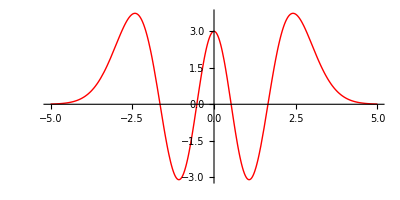

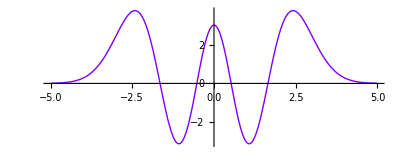

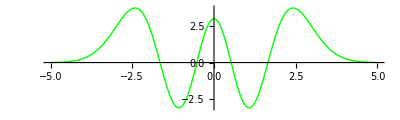

```mathematica
xmax=5;
Plot[psi,{x,-xmax,xmax},PlotStyle->{Red,Thick},AspectRatio->0.5]
Plot[psi,{x,-xmax,xmax},PlotStyle->{Hue[0.75,1,1]
,Thick},AspectRatio->0.4]
Plot[psi,{x,-xmax,xmax},PlotStyle->{RGBColor[0,1,0]
,Thick},AspectRatio->0.3]
```